```mathematica
ClearAll["Global`*"]
```

```mathematica
vv:=2
K[n_] := If[ n==1,0,FullSimplify[MangoldtLambda[n]/Log[n]]]
K2[n_] := If[ Mod[n,2]==1,0,K[n/2]]
K6[n_] := K[n]-If[ Floor[Log[vv,n]]==Log[vv,n],n /Log[vv,n],0]
P[n_,0]=1; 
P[n_, k_] := P[n,k] = Sum[ K2[j]P[Floor[n/j],k-1],{j,2,n}]
En[n_] := En[n] = Sum[ 1/(k!) P[n,k],{k,0, Log[2,n]}]
En[n_,z_] := En[n] = Sum[ (z^k)/(k!) P[n,k],{k,0, Log[2,n]}]
en[n_] := En[n]-En[n-1]
LAdd[n_] := Sum[ vv^k/k,{k,1,Log[vv,n]}]
LAdd2[n_] := Sum[(-1)^k vv^k,{k,1,Log[vv,n]}]
PP[n_,k_] := PP[n,k]=Sum[ 1/k-PP[Floor[n/j],k+1],{j,2,n}]
```

```mathematica
P[200,1]
```

428/15

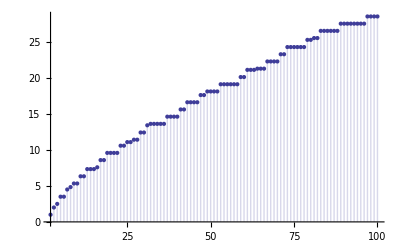

```mathematica
DiscretePlot[{P[2n,1]},{n,2,100}]
```

```mathematica
Table[{n,en[n]},{n,2,50}]//TableForm
```

2 | 1
3 | 1
4 | 1
5 | -4
6 | 1
7 | -6
8 | 1
9 | 1
10 | -4
11 | 1
12 | 1
13 | 1
14 | -6
15 | -4
16 | 1
17 | 1
18 | 1
19 | 1
20 | -4
21 | -6
22 | 1
23 | 1
24 | 1
25 | -4
26 | 1
27 | 1
28 | -6
29 | 1
30 | -4
31 | 1
32 | 1
33 | 1
34 | 1
35 | 24
36 | 1
37 | 1
38 | 1
39 | 1
40 | -4
41 | 1
42 | -6
43 | 1
44 | 1
45 | -4
46 | 1
47 | 1
48 | 1
49 | -6
50 | -4

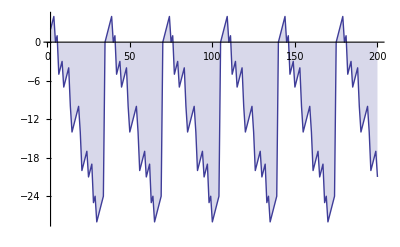

```mathematica
DiscretePlot[En[n],{n,2,200}]
```

```mathematica
Table[ {n, En[n], Mod[n,vv]},{n,1,100}]//TableForm
```

1 | 1 | 1
2 | 2 | 2
3 | 3 | 3
4 | 4 | 4
5 | 0 | 5
6 | 1 | 6
7 | -5 | 0
8 | -4 | 1
9 | -3 | 2
10 | -7 | 3
11 | -6 | 4
12 | -5 | 5
13 | -4 | 6
14 | -10 | 0
15 | -14 | 1
16 | -13 | 2
17 | -12 | 3
18 | -11 | 4
19 | -10 | 5
20 | -14 | 6
21 | -20 | 0
22 | -19 | 1
23 | -18 | 2
24 | -17 | 3
25 | -21 | 4
26 | -20 | 5
27 | -19 | 6
28 | -25 | 0
29 | -24 | 1
30 | -28 | 2
31 | -27 | 3
32 | -26 | 4
33 | -25 | 5
34 | -24 | 6
35 | 0 | 0
36 | 1 | 1
37 | 2 | 2
38 | 3 | 3
39 | 4 | 4
40 | 0 | 5
41 | 1 | 6
42 | -5 | 0
43 | -4 | 1
44 | -3 | 2
45 | -7 | 3
46 | -6 | 4
47 | -5 | 5
48 | -4 | 6
49 | -10 | 0
50 | -14 | 1
51 | -13 | 2
52 | -12 | 3
53 | -11 | 4
54 | -10 | 5
55 | -14 | 6
56 | -20 | 0
57 | -19 | 1
58 | -18 | 2
59 | -17 | 3
60 | -21 | 4
61 | -20 | 5
62 | -19 | 6
63 | -25 | 0
64 | -24 | 1
65 | -28 | 2
66 | -27 | 3
67 | -26 | 4
68 | -25 | 5
69 | -24 | 6
70 | 0 | 0
71 | 1 | 1
72 | 2 | 2
73 | 3 | 3
74 | 4 | 4
75 | 0 | 5
76 | 1 | 6
77 | -5 | 0
78 | -4 | 1
79 | -3 | 2
80 | -7 | 3
81 | -6 | 4
82 | -5 | 5
83 | -4 | 6
84 | -10 | 0
85 | -14 | 1
86 | -13 | 2
87 | -12 | 3
88 | -11 | 4
89 | -10 | 5
90 | -14 | 6
91 | -20 | 0
92 | -19 | 1
93 | -18 | 2
94 | -17 | 3
95 | -21 | 4
96 | -20 | 5
97 | -19 | 6
98 | -25 | 0
99 | -24 | 1
100 | -28 | 2

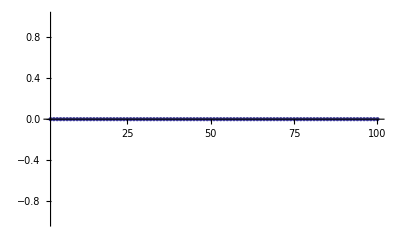

```mathematica
DiscretePlot[P[n,1]-PP[n,1]+LAdd[n]+LAdda[n],{n,2,100}]
```